# Approximating E_γ(P||Q) of product distributions

Summary

This is a visual exploration of approximating E_γ(P||Q) when P and Q are product distributions. We divide the problem into two parts:
1. First, we explore how to compute the expectation
   𝔼[f_ϵ(Z_1+Z_2+...+Z_n)], where Z_i's are i.i.d. discrete random variable and f_ϵ(x)=(1-e^(ϵ-x))^+.
2. We then focus on approximating (ϵ,δ)-curves by discrete privacy loss random variables.

## Part I: Approximating 𝔼[f_ϵ(Z_1+Z_2+...+Z_n)]

For simplicity, we start by focusing on one discrete distribution. We generate the distribution by sampling an Exponential and normalizing.

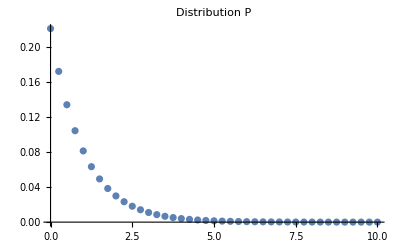

```mathematica
M = 10; (*Maximum value*)
Δ= .25;  (*Increment*)
p =Table[Exp[-x],{x,0,M,Δ}]; (*You can change this value to whatever you want*)
p = p/Total[p];
z = Range[0,10,Δ];
ListPlot[Transpose@{z,p},PlotLabel->"Distribution P",PlotRange-> {0,Max[p]}]
```

Next we view the characteristic function of our distribution. Unsurprisingly, it will be periodic with period (2π)/Δ, where Δ is the grid size.

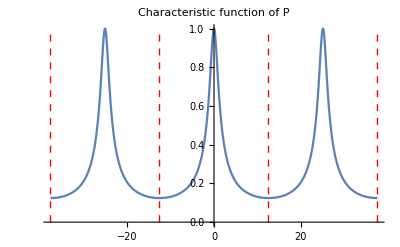

```mathematica
Cf[t_]:=Evaluate[Total[p*Exp[z*ⅈ*t]]];
lineStyle={Thick,Red,Dashed};
line1 = Line[{{-π/Δ,10^-6},{-π/Δ,1}}];
line2 = Line[{{π/Δ,10^-6},{π/Δ,1}}];
line3 = Line[{{-3π/Δ,10^-6},{-3π/Δ,1}}];
line4 = Line[{{3π/Δ,10^-6},{3π/Δ,1}}];
Plot[Abs[Cf[t]],{t,-3*π/Δ,3*π/Δ},PlotRange->{0,1},Epilog->{Directive[lineStyle],line1,line2,line3,line4},PlotLabel->"Characteristic function of P"]
```

Our goal is to compute 𝔼[f_ϵ(Z)]where Z\[Distributed]P. Of course, for one discrete variable we can do this without difficulty, as given next in the variable ExpVal.

```mathematica
f[z_,ϵ_]:=Ramp[1-Exp[ϵ-z]];
ϵval=2; (*arbitrary value of ϵ*)
ExpVal = N[Total[f[z,ϵval]*p]]
```

0.0592197

It will be useful to compute this value using the characteristic function. In this case, we use Plancherel-Parseval with the removed pole. We first compute the value of the “filter” and plot it against the characteristic function. We will also need a “tilted” version of the probability distribution. Not that the c.f. doesn’t change much -- but  it does change! It is still periodic though.

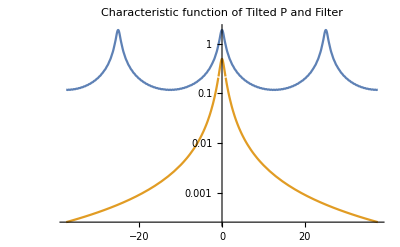

```mathematica
a = 0.5; (*arbitrary value of a*)
Filter[t_,ϵ_]:=Evaluate[Integrate[Exp[-a*x]*(1-Exp[ϵ-x])*Exp[ⅈ*t*x],{x,ϵ,∞},Assumptions-> a>0&&t∈Reals]];
pTilt = p*Exp[a*z];
CfTilt[t_]:=Evaluate[Total[pTilt*Exp[z*ⅈ*t]]];
LogPlot[{Abs[CfTilt[t]],Abs[Filter[t,ϵval]]},{t,-3*π/Δ,3*π/Δ},PlotRange->{0,2},PlotLabel->"Characteristic function of Tilted P and Filter"]
```

In order to apply Plancherel-Parseval, we will need to “fold” the integral across the period (i.e. “repeated parts”) of the characteristic function. To do this, we have to compute the “equivalent” filter within the region [-π/Δ,π/Δ].This can be precisely done in Mathematica, which is very efficient at approximating infinite sums. We plot the folded filter and the tilted characteristic function within one period.

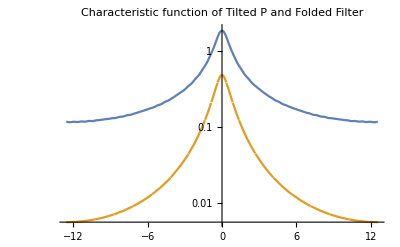

```mathematica
FoldedFilter[t_,ϵ_]:=Evaluate[FullSimplify[Sum[Filter[t+(2π*k)/Δ,ϵ],{k,-∞,∞}],Assumptions-> -π/Δ≤t≤π/Δ]];
LogPlot[{Abs[CfTilt[t]],Abs[FoldedFilter[t,ϵval]]},{t,-π/Δ,π/Δ},PlotRange->{0,2},PlotLabel->"Characteristic function of Tilted P and Folded Filter"]
```

Finally we can compute the integral using Plancherel-Parseval and see if we recover the original value.

```mathematica
NIntegrate[(CfTilt[t]*Conjugate[FoldedFilter[t,ϵval]])/(2*π),{t,-π/Δ,π/Δ}]-ExpVal
```

9.61731×10^-15

Not bad! The error is quite small. Let’s look at the error for a range of ϵ.

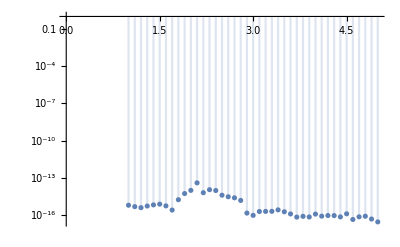

```mathematica
Approx[ϵ_]:=NIntegrate[(CfTilt[t]*Conjugate[FoldedFilter[t,ϵ]])/(2*π),{t,-π/Δ,π/Δ}];
DiscretePlot[Abs[Approx[ϵ]-Total[f[z,ϵ]*p]],{ϵ,1,5,.1},ScalingFunctions->"Log"]
```

The error is below 10^-8 across the board. This is probably in range with the integration error.
This already give a hint on how we would do this with when looking and convolution of distributions: we only need to multiply the c.f.s within one period and apply the “folded” filter. Where this might really shine is when we use the FFT.

Recall that the FFT gives a “sampled” version of the characteristic function (assuming your pmf is distributed on a lattice). The more points in the FFT (obtained by padding the distribution), the more equally spaced samples we get of the transform. Let’s illustrate that below by displaying the characteristic function and the FFT. Note that the parameters in the FFT below may be different from Matlab and Python.

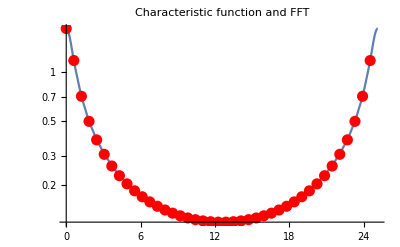

```mathematica
fft = Fourier[pTilt,FourierParameters->{1,1}];
tVals = Range[0,(2π)/Δ-(2π)/(Δ*Length[fft]),(2π)/(Δ*Length[fft])];

Show[LogPlot[{Abs[CfTilt[t]]},{t,0,2*π/Δ}],ListPlot[Transpose@{tVals,Abs[fft]},ScalingFunctions->"Log",PlotStyle->{Red,PointSize[0.02]}],PlotLabel->"Characteristic function and FFT"]
```

Importantly, the more points we take in the FFT, the finer grained the approximation. The approximation below will pad so the transform has 2^10 points

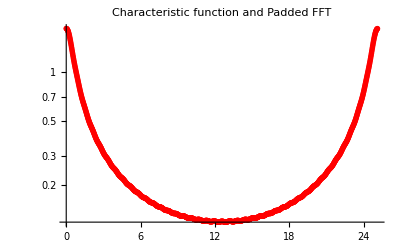

```mathematica
totalLength = 2^10;
fft = Fourier[PadRight[pTilt,totalLength-Length[pTilt]+1,0],FourierParameters->{1,1}]; (*this pads the Fourier Transform*)
tVals = Range[0,(2π)/Δ-(2π)/(Δ*Length[fft]),(2π)/(Δ*Length[fft])];

Show[LogPlot[{Abs[CfTilt[t]]},{t,0,2*π/Δ}],ListPlot[Transpose@{tVals,Abs[fft]},ScalingFunctions->"Log",PlotStyle->{Red,PointSize[0.01]}],PlotLabel->"Characteristic function and Padded FFT"]
```

Note that that we can’t even make out the function from the plot. Of course, here we are computing twice the necessary parameters due to periodicity and Hermitian symmetry. We also need to “shift” the Fourier transform to be centered around zero. In Matlab, this is done via the function fftshift(). Here, we need to use a specific function fftshift that I found on StackOverflow:

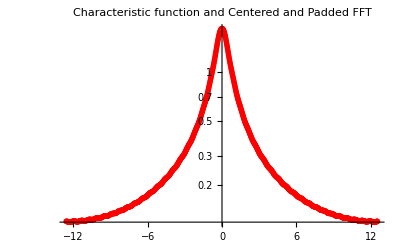

```mathematica
fftshift[dat_?ArrayQ,k:(_Integer?Positive|All):All]:=Module[{dims=Dimensions[dat]},RotateRight[dat,If[k===All,Quotient[dims,2],Quotient[dims[[k]],2] UnitVector[Length[dims],k]]]];
ffts = fftshift[fft];
tVals = Range[-π/Δ,π/Δ-(2π)/(Δ*Length[ffts]),(2π)/(Δ*Length[ffts])];
Show[LogPlot[{Abs[CfTilt[t]]},{t,-π/Δ,π/Δ}],ListPlot[Transpose@{tVals,Abs[ffts]},ScalingFunctions->"Log",PlotStyle->{Red,PointSize[0.01]}],PlotLabel->"Characteristic function and Centered and Padded FFT"]
```

Now we can compute a discrete/Riemann approximation of the  transform times the filter.

```mathematica
sampledFilter = Conjugate[FoldedFilter[tVals,ϵval]]/(2*π);
Estimate = Re[Total[sampledFilter*ffts]*((2π)/(Δ*Length[ffts]))]-ExpVal
```

1.52656×10^-16

This error is LOWER than the numerical integration given by Mathematica. The bottleneck is computing the folded filter, but that is something we only need to do once in composition. Also note that we aren’t even using that many samples of the FFT... Let’s do an error plot as before.

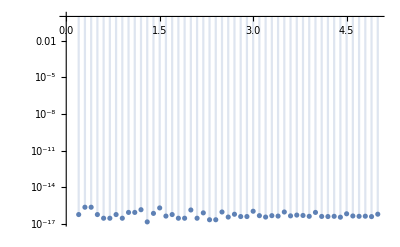

```mathematica
ApproxFFT[ϵ_]:=Re[Total[ Conjugate[FoldedFilter[tVals,ϵ]]*ffts]*(1/(Δ*Length[ffts]))];
DiscretePlot[Abs[ApproxFFT[ϵ]-Total[f[z,ϵ]*p]],{ϵ,0.1,5,.1},ScalingFunctions->"Log"]
```

Finally, for independent composition we can now simply take the product of the FFTs and apply the folded filter. For i.i.d. distributions, we can simply take the power of the FFTs (something we cannot do if we rely on convolution). Here is one plot for the product of 5 distributions. Of course, this will not resemble E_γ since this is just an arbitrary distribution.

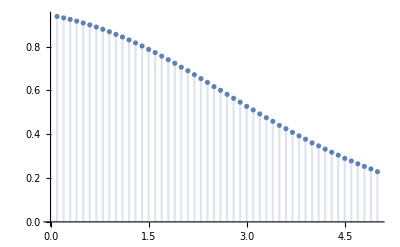

```mathematica
ApproxFFT[ϵ_,n_]:=Re[Total[ Conjugate[FoldedFilter[tVals,ϵ]]*ffts^n]*(1/(Δ*Length[ffts]))];
DiscretePlot[Re[ApproxFFT[ϵ,5]],{ϵ,0.1,5,.1}]
```

We compare with exact computation for composition n=2 (I chose this value because Mathematica is slow when computing higher ). There should be no difference between the plots.

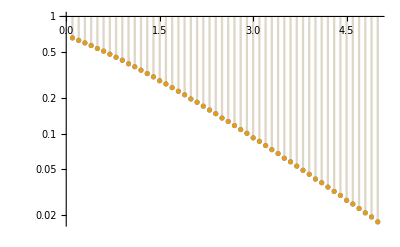

```mathematica
P = EmpiricalDistribution[p-> z];
P2 =TransformedDistribution[x1+x2,{x1\[Distributed]P,x2\[Distributed]P}];
ESum[ϵ_]:=Evaluate[Expectation[Ramp[1-Exp[ϵ-x]],x\[Distributed]P2]];
DiscretePlot[{Re[ApproxFFT[ϵ,2]],ESum[ϵ]},{ϵ,0.1,5,.1},ScalingFunctions->"Log"]
```

Now we check the error with n=3 (may take a long depending on how many point are in the distribution). The missing values actually evaluate to 0 (as far as I can tell ;).

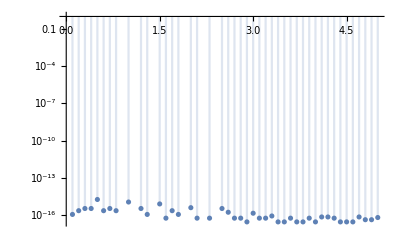

```mathematica
P = EmpiricalDistribution[p-> z];
P3 =TransformedDistribution[x1+x2+x3,{x1\[Distributed]P,x2\[Distributed]P,x3\[Distributed]P}];
ESum[ϵ_]:=Evaluate[Expectation[Ramp[1-Exp[ϵ-x]],x\[Distributed]P3]];
DiscretePlot[Abs[Re[ApproxFFT[ϵ,3]]-ESum[ϵ]],{ϵ,0.1,5,.1},ScalingFunctions->"Log"]
```

To-do list based on the above discussion. This is in no particular order.

1. We need to understand how the number of points in the fft, the number of compositions, and properties of the discrete distribution (support, variation, etc.) impact the final result. It may be the case that the number of points in the FFT is linked to the number of compositions since more compositions → more precision. We may need to explore this further. However, these preliminary results are encouraging, and the number of computations may be close to O(n), where n is the number of compositions.
2. The “folded” filter depends on the choice of ϵ and the choice of a (i.e., the value that removes the pole). The points at which the folded filter are evaluated also depend on the chosen quantization. The filter only needs to be computed once. This is how it looks like for arbitrary a:

```mathematica
Clear[a]
FilterA[t_,ϵ_,a_]:=Evaluate[Integrate[Exp[-a*x]*(1-Exp[ϵ-x])*Exp[ⅈ*t*x],{x,ϵ,∞},Assumptions-> a>0&&t∈Reals]];
FullSimplify[Sum[FilterA[t+(2π*k)/Δ1,ϵ,a],{k,-∞,∞}],Assumptions-> -π/Δ1≤t≤π/Δ1,Assumptions-> Δ1>0&&-π/Δ1≤t≤π/Δ1&&ϵ∈Reals&&a>0]
```

1/(2 π)ⅈ ⅇ^(-a ϵ+ⅈ t ϵ) Δ1 ((ⅇ^(-(2 ⅈ π ϵ)/Δ1))^(((ⅈ (1+a)+t) Δ1)/(2 π)) Beta[ⅇ^(-(2 ⅈ π ϵ)/Δ1),1-(ⅈ (1+a-ⅈ t) Δ1)/(2 π),0]-(ⅇ^(-(2 ⅈ π ϵ)/Δ1))^(((ⅈ a+t) Δ1)/(2 π)) Beta[ⅇ^(-(2 ⅈ π ϵ)/Δ1),1-((ⅈ a+t) Δ1)/(2 π),0]+(ⅇ^((2 ⅈ π ϵ)/Δ1))^(-((ⅈ a+t) Δ1)/(2 π)) Beta[ⅇ^((2 ⅈ π ϵ)/Δ1),((ⅈ a+t) Δ1)/(2 π),0]-(ⅇ^((2 ⅈ π ϵ)/Δ1))^(-((ⅈ (1+a)+t) Δ1)/(2 π)) Beta[ⅇ^((2 ⅈ π ϵ)/Δ1),((ⅈ (1+a)+t) Δ1)/(2 π),0])

The expression above is the folded filter. Note that the value above is “closed form” in the sense that we can compute it given that we can approximate Hypergeometric functions arbitrarily well. 
3. Implement and test this in Python/Matlab.

## Part II: Approximating (ϵ,δ)-curves by discrete privacy loss random variables

We now explore how to derive discrete privacy loss random variables based on a collection of pairs (γ,E_γ). Ideally, we would apply this technique to derive privacy loss r.v.s and plug it in to the approach in Part I. For the FFT to work out of the box, the curve needs to be sampled in equal spaces in Log[γ] (i.e., ϵ). But this is just an initial exploration.
We explore the Gaussian Case. We plot the E_γcurve for two Gaussians shifted by 1 with unit variance.

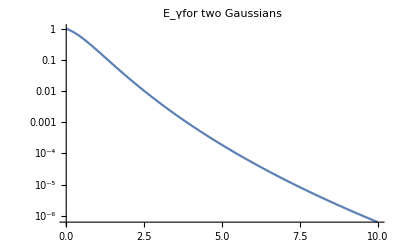

```mathematica
Eg[γ_,σ_]:=1/2 (Erfc[(-1+2 σ^2 Log[γ])/(2 √2 σ)]-γ Erfc[(1+2 σ^2 Log[γ])/(2 √2 σ)]);
LogPlot[Eg[γ,2],{γ,0,10},PlotRange-> {0,1},PlotLabel->"E_γfor two Gaussians"]
```

We sample the curve up to a maximum value of G with sampling spaces of h. The values are stored in the list l. We repeat the final value of l since this will be useful for computing the equivalent p.l.r.v.

```mathematica
h = .1;
G = 20;
l = Table[Limit[Eg[x,2],x-> γ],{γ,0,G,h}];
l = Append[l,l[[-1]]];
```

Using the result in Yury’s thesis, we can compute two discrete distributions p and q whose E_γ divergence is an  upper bound the original curve. This is done in the next code. Note that we have to add two additional points so that everything adds up to one. Note that these are points where either p or q are 0. We will deal with this later.

```mathematica
q = Differences[l,2]/h; (*q is derived from the difference in derivatives*)
p = q*Range[h,G,h]; (*p is proportional to q*)
q = Append[q,0];
p = Append[p,1-Total[p]]; (*added so stuff adds up to one*)
p = Append[p,0];
q = Append[q,1-Total[q]];  (*added so stuff adds up to one*)
Egd[γ_]:=Total[Ramp[p-γ*q]];   (*Discrete Subscript[E, γ]*)
```

We plot both E_γ curves next. Note how the discrete version “tapers off” at the maximum range -- that’s why it is a true upper bound.

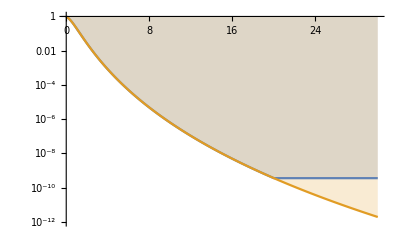

```mathematica
DiscretePlot[{Egd[γ],Eg[γ,2]},{γ,0,1.5*G,h/20},PlotRange->{10^-12,1},ScalingFunctions->"Log"]
```

We plot next the error between the discrete approximation and the blue curves just to make sure it is correct (this difference should be very small).

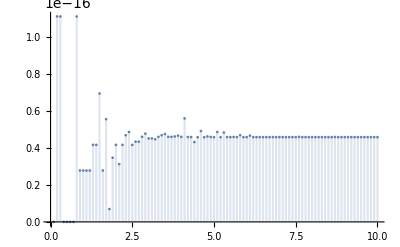

```mathematica
DiscretePlot[Abs[(Egd[γ]-Eg[γ,2])],{γ,h,10,h},PlotRange->Full]
```

Here is the plot of p and q:

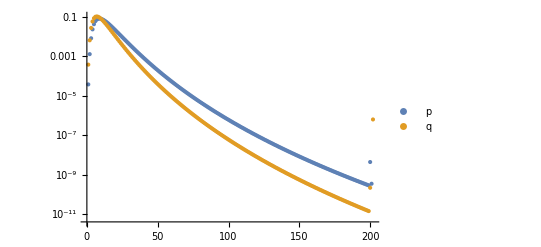

```mathematica
ListPlot[{p,q},PlotRange->Full,PlotLegends->{"p","q"},ScalingFunctions->"Log"]
```

Finally, here is the ration of p/q -- unsurprisingly, it’s exactly the evaluation points we chose for the original E_γ curve.

```mathematica
p/q
```

Power::infy: Infinite expression 1/0 encountered.

{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.,10.1,10.2,10.3,10.4,10.5,10.6,10.7,10.8,10.9,11.,11.1,11.2,11.3,11.4,11.5,11.6,11.7,11.8,11.9,12.,12.1,12.2,12.3,12.4,12.5,12.6,12.7,12.8,12.9,13.,13.1,13.2,13.3,13.4,13.5,13.6,13.7,13.8,13.9,14.,14.1,14.2,14.3,14.4,14.5,14.6,14.7,14.8,14.9,15.,15.1,15.2,15.3,15.4,15.5,15.6,15.7,15.8,15.9,16.,16.1,16.2,16.3,16.4,16.5,16.6,16.7,16.8,16.9,17.,17.1,17.2,17.3,17.4,17.5,17.6,17.7,17.8,17.9,18.,18.1,18.2,18.3,18.4,18.5,18.6,18.7,18.8,18.9,19.,19.1,19.2,19.3,19.4,19.5,19.6,19.7,19.8,19.9,20.,ComplexInfinity,0.}

You may look at the 1/0 value and be distressed. But worry not! There is a easy fix for it. When computing E_γ using a privacy loss random variable, we can simply isolate that value. Denote the distribution by (p_1,...,p_M) and (q_1,...,q_M) and assume there is one j such that p_j≠ 0 and q_j=0. Then
E_γ(p || q) = p_j+∑_(i≠ j) (p_j(1-e^(Log[γ]-p_j/q_j)))^+
When doing composition, the term outside of the sum becomes (1-(1-p_(1j))(1-p_(2j))...) and we can consider only the values for which the p.l.r.v. is well defined inside the sum.

To-do list based on the above discussion. This is in no particular order.

1. The sampling above needs to be uniform in Log[γ], not γ.
2. Characterize the error in approximating the E_γ curve. Doing composition with the upper-bounding curve yields an upper bound, but it would be nice to control the error. How many values of γ do we need?
3. When does a sequence of measurement (γ_k,δ_k) yield valid distributions p and q? Will this work if we get the upper bounding curves of two E_γcurves, for example?
4. Most importantly, combine Parts I and II.